## DIRK - Diagonally Implicit Runge–Kutta methods

Francesco Torsello

References
[1] J. C. Butcher, Numerical Methods for Ordinary Differential Equations, John Wiley & Sons, 2008, ISBN: 9780470753750
[2] NASA, Diagonally Implicit Runge-Kutta Methods for Ordinary Differential Equations. A Review. https://ntrs.nasa.gov/archive/nasa/casi.ntrs.nasa.gov/20160005923.pdf
[3] Stål, Josefine, Implementation of Singly Diagonally Implicit Runge-Kutta Methods with Constant Step Sizes, Bachelor’s Theses in Mathematical Sciences, 2015, ISSN: 1654-6229, http://lup.lub.lu.se/student-papers/record/7851608

[4] A. Kværnø, S.P. Nørsett, B. Owren, Runge-Kutta research in Trondheim, Applied Numerical Mathematics, Volume 22, Issues 1–3, 1996, pp. 263-277, ISSN 0168-9274, https://doi.org/10.1016/S0168-9274(96)00037-2

[5] Kværnø, Singly Diagonally Implicit Runge–Kutta Methods with an Explicit First Stage, A.BIT Numerical Mathematics (2004) 44 : 489. https : // doi.org/10.1023/B : BITN .0000046811 .70614 .38

Useful links
[6] https://en.wikipedia.org/wiki/List_of_Runge % E2 %80 %93 Kutta_methods

### Introduction

From [1],

-Graphics-

and from the introduction of [2],

-Graphics-

-Graphics-

### The chosen DIRK method

We take the following two excerpts from [4],

-Graphics-

-Graphics-

#### ESDIRK 3/2 with s=4 stages, L-stable, embedded (but there is no adaptive time step here)

The implemented ESDIRK method is taken from [5, p.497]. Defining the vectors c

-Graphics-

```mathematica
c={{0},{2γ},{1},{1}};
```

```mathematica
A={
{0,0,0,0},
{γ,γ,0,0},
{(-4 γ^2+6γ-1)/(4γ),(-2γ+1)/(4γ),γ,0},
{(6γ-1)/(12γ),-1/(12(2γ-1)γ),(-6 γ^2+6γ-1)/(6γ-3),γ}
};
```

```mathematica
ESDIRK32=MapThread[Join,{c,A}];
```

```mathematica
ESDIRK32$BT=Grid[ESDIRK32,Dividers->{{False,True},False}]
```

0 | 0 | 0 | 0 | 0
2 γ | γ | γ | 0 | 0
1 | (-1+6 γ-4 γ^2)/(4 γ) | (1-2 γ)/(4 γ) | γ | 0
1 | (-1+6 γ)/(12 γ) | -1/(12 γ (-1+2 γ)) | (-1+6 γ-6 γ^2)/(-3+6 γ) | γ

The parameter γ is set by solving the condition for L-stability for it [5, p.497]. We propagate  to the next step the value computed in the last line of A, hence the number of stages (i.e., the number of intermediate steps within one time step) is s=4 [5, p.497].

```mathematica
s=4;
```

```mathematica
LStability[s_]:=Γ^(s-1)LaguerreL[s-1,1/Γ]==0
```

```mathematica
LStability[s]//Simplify
```

9 Γ+6 Γ^3==1+18 Γ^2

```mathematica
NSolve[LStability[4],Γ,Reals,WorkingPrecision->30]
```

{{Γ→0.158983899988676546782594777575},{Γ→0.435866521508458999416019451194},{Γ→2.40514957850286445380138577123}}

```mathematica
γ=NSolve[LStability[4],Γ,Reals,WorkingPrecision->30]⟦2,1,2⟧;
```

```mathematica
ESDIRK32$BT
```

0 | 0 | 0 | 0 | 0
0.871733043016917998832038902387 | 0.435866521508458999416019451194 | 0.435866521508458999416019451194 | 0 | 0
1 | 0.49056338842178057062846795847 | 0.07357009006976042995551259034 | 0.435866521508458999416019451194 | 0
1 | 0.30880996997674652334816246989 | 1.4905633884217805706284679585 | -1.23523987990698609339264988 | 0.435866521508458999416019451194

One nonlinear equation

### The differential equation and its exact solution

Here we define the differential equation to integrate and find its exact solution.

```mathematica
Clear[f];
f[t_,r_,y_]:=y^2/((1+y)r) ⅇ^(-t^2);
```

```mathematica
DSolve[{D[y[t,r],t]==y[t,r]^2/((1+y[t,r])r) ⅇ^(-t^2),y[0,r]==2.43763},{y[t,r]},{t,r}]⟦1,1,2⟧//Quiet
```

1/ProductLog[ⅇ^(-0.480792-(√π Erf[t])/(2 r))]

```mathematica
Clear[ExactSolution];
ExactSolution[t_,r_]:=1/ProductLog[ⅇ^(-0.4807917247196075-(√π Erf[t])/(2 r))]
```

### Numerical solution of the equation

To solve the system, we need to compute a Jacobian matrix at each stage. The components of this Jacobian are the derivatives of the right-hand side of the evolution equations evaluated at the stage values of the unkown variables, with respect to the values of the variables at the previous stage.

This excerpt is taken from [2],

-Graphics-

```mathematica
m=1;                                                             (* number of unkown variables *)
r0=1;                                                          (* fixed radius or collocation point *)
t0=0;                                                          (* initial time *)
h=0.01;                                                     (* time step *)
t[0]=t0;
y[0]=2.43763;                                       (* initial data *)
𝕀[1]=1;                                                   (* utility function *)
𝕀[m_]:=IdentityMatrix[m];
```

Y[n,i][k] means value of the variable Y at time step n, stage i and iteration k.

```mathematica
Clear[step$n$stage$i];
step$n$stage$i[n_,i_]:=y[n]+h Sum[A⟦i,j⟧f[t[n]+c⟦j,1⟧h,r0, Y[n,j]],{j,1,s}]//Simplify
```

Compare the above formula with (81) in the last excerpt.

Now we compute the Jacobian, and keep it the same for all time steps (it should be updated after some time).

```mathematica
Clear[J];
J[n_]:=D[f[t[np],r0,step$n$stage$i[np,1]],y[np]]/.{np->n}
```

We define the matrix ℕ in (83).

```mathematica
ℕ[n_,i_]:=𝕀[m]-h A⟦i,i⟧J[n]
```

Now we are set the initial data.

```mathematica
Y[0,1][0]=y[0]+0.05436h;
```

At this point, we write the functions to perform the modified Newton iteration at each stage (the following functions are at a fixed r or collocation point).

In C++, the LU decomposition has to be implemented in the following loop. Here in Mathematica, we just use Solve. The following loop performs the Newton iteration for a given stage,

```mathematica
tol=10^-4;
```

```mathematica
Clear[computeStage];
computeStage[n_,i_,tolerance_]:=Module[{dis,k},
dis=10^3;
k=0;
While[Abs[dis]>tolerance,
dis=Solve[
	ℕ[n,i]x==-(Y[n,i][k]-y[n])+h Sum[A⟦i,j⟧f[t[n]+c⟦j,1⟧h,r0, Y[n,j][n$iteration[j]]],{j,1,i-1}]
			  +h  Sum[A⟦i,s⟧f[t[n]+c⟦s,1⟧h,r0, Y[n,s][k]],{j,i,s}],
x]⟦1,1,2⟧;
Y[n,i][k+1]=Y[n,i][k]+dis;
++k;
];
n$iteration[i]=k-1;
Y[n,i+1][0]=Y[n,i][k-1];
]
```

The following function performs the loop over the stages within a time step,

```mathematica
Clear[computeStep];
computeStep[n_,tol_]:=Module[{σ},
For[σ=1,σ≤s,σ++,
computeStage[n,σ,tol];
];
y[n+1]=Y[n,σ][0];
Y[n+1,1][0]=Y[n,σ][0];
]
```

The following loop finally integrates up until t_1,

```mathematica
Clear[integrate];
integrate[t0_,t1_,tol_]:=Module[{m},
m=0;
t[0]=t0;
Monitor[
While[t[m]≤t1,
computeStep[m,tol];
t[m+1]=t[m]+h;
++m;
],
t[m]];
m$size=m-1;
Print["Integration performed from t="<>ToString[t0]<>" to t="<>ToString[t1]<>" in m="<>ToString[m$size]<>" steps."];
]
```

Now comes the actual integration,

```mathematica
h=0.01;
integrate[0,10,tol]
```

Integration performed from t=0 to t=10 in m=1000 steps.

We compare the numerical solution (blue) with the exact solution (red dashed),

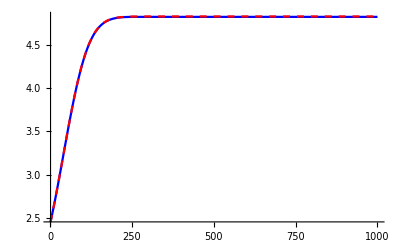

```mathematica
DiscretePlot[
{y[n],ExactSolution[t[n],r0]},
{n,1,m$size},
PlotRange->Full,
PlotStyle->{Blue,{Red,Dashed}},
Filling->None,
Joined->True
]
```

Numerical and exact solution coincide over the entire range. Note, however, that if we choose a time step h 10 times smaller, and integrate,

```mathematica
h=0.001;
integrate[0,10,tol]
```

Integration performed from t=0 to t=10 in m=10000 steps.

we obtain the following numerical solution (blue),

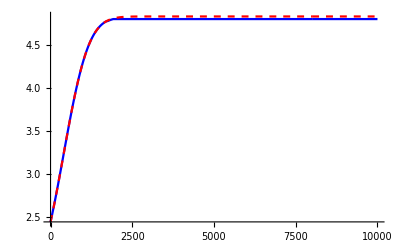

```mathematica
DiscretePlot[
{y[n],ExactSolution[t[n],r0]},
{n,1,m$size},
PlotRange->Full,
PlotStyle->{Blue,{Red,Dashed}},
Filling->None,
Joined->True
]
```

which is not as good as the previous one! Perhaps this happens because we don’t update the value of the Jacobian over a much larger number of steps.

A nonlinear system of two equation

### The differential system and its exact solution

Here we define the differential equation to integrate and find its exact solution.

```mathematica
ClearAll[x,y,z,X,F,f,g];
```

```mathematica
Clear[f,g];
f[y_,z_]:=-z y;
g[y_]:=y;
```

```mathematica
DSolve[{
D[y[t,r0],t]==-z[t,r0]y[t,r0],
D[z[t,r0],t]==y[t,r0],                      (* equations *)

y[0,r0]==0.4524,
z[0,r0]==0.7644                                           (* Initial data *)

},{y[t,r0],z[t,r0]},{t}]//Simplify//Quiet//Echo/@#&;
```

{z[t,1]→1.22029 √(Tanh[0.735483-0.610145 t]^2),y[t,1]→0.744554-0.744554 Tanh[0.735483-0.610145 t]^2}

{z[t,1]→1.22029 √(Tanh[0.735483+0.610145 t]^2),y[t,1]→0.744554-0.744554 Tanh[0.735483+0.610145 t]^2}

```mathematica
Clear[x];
x[n_]={y[n],z[n]};
```

```mathematica
Clear[F];
F[t_,r_,{y_,z_}]:={f[y,z],g[y]};
```

```mathematica
Clear[ExactSolution];
ExactSolution[t_]:={0.74455368-0.74455368 Tanh[0.7354833408382715+0.6101449336018452 t]^2,1.2202898672036904 √(Tanh[0.7354833408382715+0.6101449336018452 t]^2)}
```

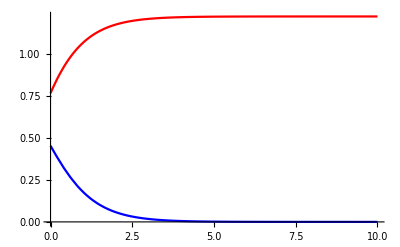

```mathematica
Plot[{0.74455368-0.74455368 Tanh[0.7354833408382715+0.6101449336018452 t]^2,1.2202898672036904 √(Tanh[0.7354833408382715+0.6101449336018452 t]^2)},{t,0,10},PlotStyle->{Blue,Red}]
```

### The numerical integration of the system

```mathematica
v=2;                                                             (* number of unkown variables *)
r0=1;                                                          (* fixed radius or collocation point *)
t0=0;                                                          (* initial time *)
h=0.01;                                                     (* time step *)
t[0]=t0;
y[0]=0.4524;
z[0]=0.7644;                                       (* initial data *)
𝕀[1]=1;                                                   (* utility function *)
𝕀[m_]:=IdentityMatrix[m];
```

Y[n,i][k] means value of the variable Y at time step n, stage i and iteration k.

```mathematica
Clear[step$n$stage$i];
step$n$stage$i[n_,i_]:=x[n]+h Sum[A⟦i,j⟧F[t[n]+c⟦j,1⟧h,r0, Y[n,j]],{j,1,s}]//Simplify
```

Compare the above formula with (81) in the last excerpt.

Now we compute the Jacobian, and keep it the same for all time steps (it should be updated after some time).

```mathematica
Clear[J];
J[n_]:={
{D[F[t[np],r0,step$n$stage$i[np,1]]⟦1⟧,y[np]]/.{np->n}, 
D[F[t[np],r0,step$n$stage$i[np,1]]⟦1⟧,z[np]]/.{np->n}},
{D[F[t[np],r0,step$n$stage$i[np,1]]⟦2⟧,y[np]]/.{np->n},
D[F[t[np],r0,step$n$stage$i[np,1]]⟦2⟧,z[np]]/.{np->n}}
}
```

```mathematica
J[0]//MatrixForm
```

(-0.7644 | -0.4524
1 | 0)

We define the matrix ℕ in (83).

```mathematica
ℕ[n_,i_]:=𝕀[v]-h A⟦i,i⟧J[n]
```

Now we are set the initial data. X at time 0, stage 1, iteration 0 is equal to the initial data,

```mathematica
X[0,1][0]={0.4524,0.7644};
```

At this point, we write the functions to perform the modified Newton iteration at each stage (the following functions are at a fixed r or collocation point).

In C++, the LU decomposition has to be implemented in the following loop. Here in Mathematica, we just use Solve. The following loop performs the Newton iteration for a given stage,

```mathematica
tol=10^-4;
```

```mathematica
Clear[computeStage];
computeStage[n_,i_,tolerance_]:=Module[{dis$y,dis$z,k},
dis$y=10^3;
dis$y=10^3;
k=0;
While[(Abs[dis$y]>tolerance || Abs[dis$z]>tolerance)&&k<100,
{dis$y,dis$z}=Solve[
ℕ[n,i].{xx,yy}==-(X[n,i][k]-x[n])+h Sum[A⟦i,j⟧F[t[n]+c⟦j,1⟧h,r0, X[n,j][n$iteration[j]]],{j,1,i-1}]
    +h  Sum[A⟦i,s⟧F[t[n]+c⟦s,1⟧h,r0, X[n,s][k]],{j,i,s}],{xx,yy}
]⟦1,All,2⟧;
X[n,i][k+1]=X[n,i][k]+{dis$y,dis$z};
++k;
];
n$iteration[i]=k-1;
X[n,i+1][0]=X[n,i][k-1];
]
```

The following function performs the loop over the stages within a time step,

```mathematica
Clear[computeStep];
computeStep[n_,tol_]:=Module[{σ},
For[σ=1,σ≤s,σ++,
computeStage[n,σ,tol];
];
x[n+1]=X[n,σ][0];
y[n+1]=X[n,σ][0]⟦1⟧;
z[n+1]=X[n,σ][0]⟦2⟧;
X[n+1,1][0]=X[n,σ][0];
]
```

The following loop finally integrates up until t_1,

```mathematica
Clear[integrate];
integrate[t0_,t1_,tol_]:=Module[{m},
m=0;
t[0]=t0;
Monitor[
While[t[m]≤t1,
computeStep[m,tol];
t[m+1]=t[m]+h;
++m;
],
t[m]];
m$size=m-1;
Print["Integration performed from t="<>ToString[t0]<>" to t="<>ToString[t1]<>" in m="<>ToString[m$size]<>" steps."];
]
```

Now comes the actual integration,

```mathematica
h=0.01;
integrate[0,10,tol]
```

Integration performed from t=0 to t=10 in m=1000 steps.

We compare the numerical solution (blue) with the exact solution (red dashed),

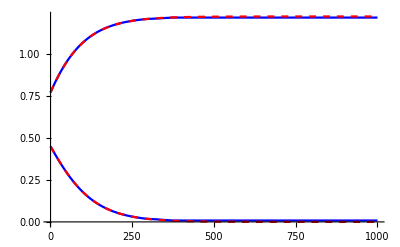

```mathematica
DiscretePlot[
{x[m],ExactSolution[t[m]]},
{m,1,m$size},
PlotRange->Full,
PlotStyle->{Blue,{Red,Dashed}},
Filling->None,
Joined->True
]
```

Numerical and exact solution coincide over the entire range.

I played a little bit with the time step. It seems that the smaller the time step, the smaller should be the tolerance in order to get an accurate solution. For example,

Here the time step is h=10^-3  and the tolerance is tol=10^-4 (same tolerance as before, but h → h/10),

Integration performed from t=0 to t=10 in m=10000 steps.

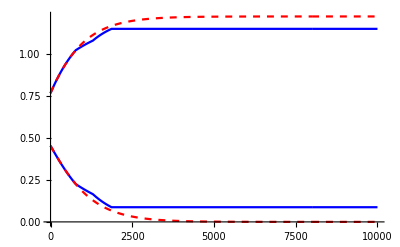

```mathematica
h=0.001;
integrate[0,10,tol]
DiscretePlot[
{x[m],ExactSolution[t[m]]},
{m,1,m$size},
PlotRange->Full,
PlotStyle->{Blue,{Red,Dashed}},
Filling->None,
Joined->True
]
```

The above result is not nice. Now we try the same time step as abopve, but a tolerance of 10^-5= tol/10.

Integration performed from t=0 to t=10 in m=10000 steps.

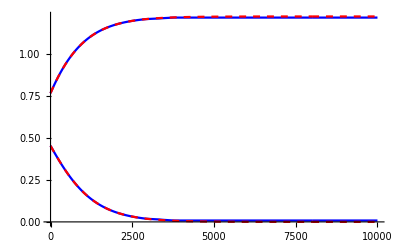

```mathematica
h=0.001;
integrate[0,10,10^-5]
DiscretePlot[
{x[m],ExactSolution[t[m]]},
{m,1,m$size},
PlotRange->Full,
PlotStyle->{Blue,{Red,Dashed}},
Filling->None,
Joined->True
]
```

This is better, and comparable with h=10^-2, tol=10^-4! Hence, the dependence seems to be linear. Let’s try with even smaller tolerance,

Integration performed from t=0 to t=10 in m=10000 steps.

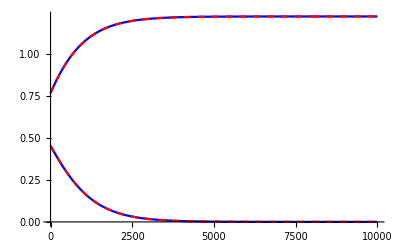

```mathematica
h=0.001;
integrate[0,10,10^-8]
DiscretePlot[
{x[m],ExactSolution[t[m]]},
{m,1,m$size},
PlotRange->Full,
PlotStyle->{Blue,{Red,Dashed}},
Filling->None,
Joined->True
]
```